## 13 TeV Plot m_H - tanβ

### Frame

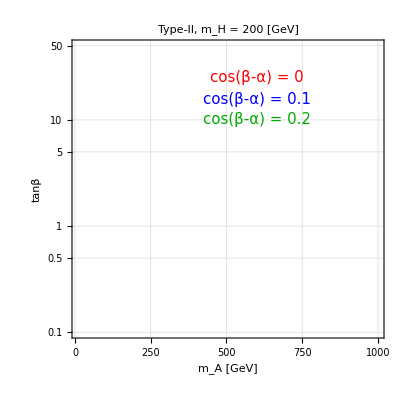

```mathematica
(*Create a nice looking Frame*)
SetOptions[ListPlot,BaseStyle->{FontSize->15}];
ticksyaxis = { 
 {Log10[0.1],"0.1"(*Superscript[10,-1]*)},{Log10[0.2],""},{Log10[0.3],""},{Log10[0.4],""},
{Log10[0.5],"0.5"},{Log10[0.6],""},{Log10[0.7],""},{Log10[0.8],""},{Log10[0.9],""},
 {Log10[1],1},{Log10[2],""},{Log10[3],""},{Log10[4],""},
{Log10[5],"5"},{Log10[6],""},{Log10[7],""},{Log10[8],""},{Log10[9],""},
 {Log10[10],10},{Log10[20],""},{Log10[30],""},{Log10[40],""},
{Log10[50],"50"},{Log10[60],""},{Log10[70],""},{Log10[80],""},{Log10[90],""},
 {Log10[100],100}};
MyFramecos=ListPlot[{{-10,-1},{-20,-1}},
PlotRange->{{xmin,xmax},{ymin,ymax}},
Frame->True, Axes->False,AspectRatio->1,FrameStyle->Directive[Black,Thick],
Joined->True,Filling->None,
GridLines->Automatic,
FrameTicks->{{ticksyaxis,None},{Automatic,None}},
FrameLabel->{Style["m_A [GeV]",Black,21],Style["tanβ",Black,21]},
PlotLabel->Style["Type-II, m_H = 200 [GeV]",Black,18],
Epilog->{
Inset[Style["cos(β-α) = 0",Red,15],{600,Log10[25]}],
Inset[Style["cos(β-α) = 0.2",Darker[Green],15],{600,Log10[10]}],
Inset[Style["cos(β-α) = 0.1",Blue,15],{600,Log10[15.7]}]

},
ImageSize->400]
```

### color set

RGBColor[1, 0, 0]

RGBColor[Rational[253, 255], Rational[103, 255], Rational[103, 255]]

RGBColor[Rational[48, 85], Rational[14, 15], Rational[48, 85]]

RGBColor[Rational[9, 17], Rational[206, 255], Rational[50, 51]]

RGBColor[1, Rational[28, 51], 0]

RGBColor[1, Rational[44, 51], Rational[2, 3]]

RGBColor[Rational[16, 17], Rational[44, 51], Rational[2, 51]]

RGBColor[Rational[49, 51], Rational[49, 51], Rational[10, 17]]

RGBColor[0, 1, 1]

RGBColor[Rational[203, 255], Rational[253, 255], Rational[253, 255]]

RGBColor[0.5, 0, 0.5]

RGBColor[Rational[13, 15], Rational[32, 51], Rational[13, 15]]

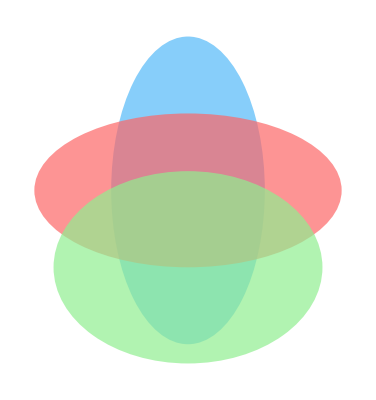

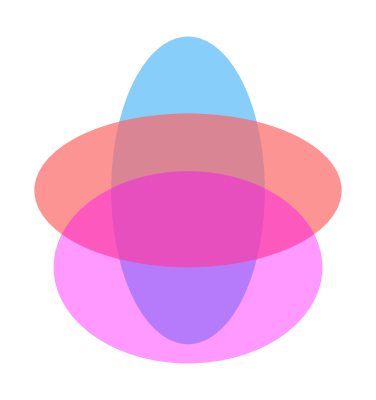

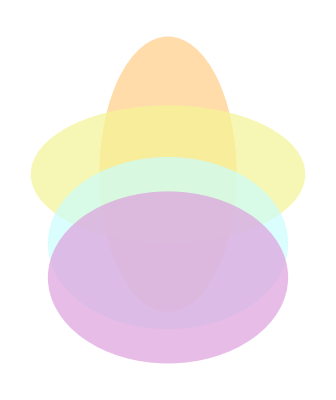

```mathematica
Red
clightred(*fd6767*)=RGBColor[253/255,103/255,103/255]
clightgreen=RGBColor[144/255,238/255,144/255]
clightskyblue=RGBColor[135/255,206/255,250/255]
orange=RGBColor[255/255,140/255,0/255]
clightorange=RGBColor[255/255,220/255,170/255]
yellow=RGBColor[240/255,220/255,10/255]

clightyellow=RGBColor[245/255,245/255,150/255]
Cyan
clightcyan=RGBColor[203/255,253/255,253/255]
Purple
clightpurple=RGBColor[221/255,160/255,221/255]


Graphics[{Directive[clightskyblue,Opacity[1] ],Disk[{0,0},{2,4}],Directive[clightred,Opacity[0.7] ],Disk[{0,0},{4,2}],Directive[clightgreen,Opacity[0.7] ],Disk[{0,-2},{3.5,2.5}]}]
Graphics[{Directive[clightskyblue,Opacity[1] ],Disk[{0,0},{2,4}],Directive[clightred,Opacity[0.7] ],Disk[{0,0},{4,2}],Directive[Magenta,Opacity[0.4] ],Disk[{0,-2},{3.5,2.5}]}]
Graphics[{Directive[clightorange,Opacity[1] ],Disk[{0,0},{2,4}],Directive[clightyellow,Opacity[0.7] ],Disk[{0,0},{4,2}],Directive[clightcyan,Opacity[0.7] ],Disk[{0,-2},{3.5,2.5}],Directive[clightpurple,Opacity[0.7] ],Disk[{0,-3},{3.5,2.5}]}]
```

double lim[exp_len]={lim_ggAzhbb,lim_bbAzhbb,lim_ppHZZ,lim_ppHhh,lim_ggHWW,lim_VBFHWW, \6
        lim_bbHbb,lim_bbHmumu,lim_ggHmumu,lim_bbHtautau,lim_ggHtautau,\5
        lim_bbAbb,lim_bbAmumu,lim_ggAmumu,lim_bbAtautau,lim_ggAtautau,\5
        lim_ggAZHbb,lim_bbAZHbb,lim_Htt,lim_Att,lim_ppAyy8,lim_ppHyy8,\6
        lim_Ayy13,lim_Hyy13,lim_bbA2tau,lim_haa2b2mu,lim_haa2b2tau,lim_haa4tau};6

### Type-I, m_A=m_H, cos(β-α)=0.1,Brhaa

RGBColor[Rational[253, 255], Rational[103, 255], Rational[103, 255]]

RGBColor[Rational[48, 85], Rational[14, 15], Rational[48, 85]]

RGBColor[Rational[9, 17], Rational[206, 255], Rational[50, 51]]

/Users/weisu/Documents/research/project/114a/LHC_HZA/1new_code/My2HDMC0408/data_mh2tb/4top/

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36.0527,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {49.079,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

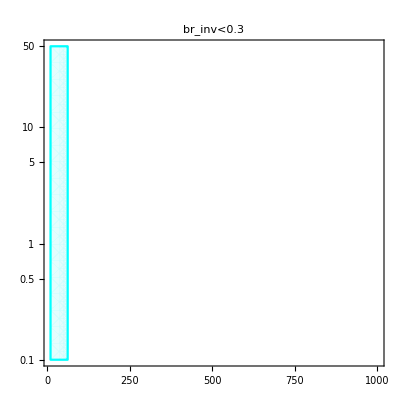

```mathematica
clightred(*fd6767*)=RGBColor[253/255,103/255,103/255]
clightgreen=RGBColor[144/255,238/255,144/255]
clightskyblue=RGBColor[135/255,206/255,250/255]
PathDir=NotebookDirectory[]

(*DEFINE SETUP*)
xmin=10;xmax=1000;ymin=Log10[0.1];ymax=Log10[50];

(*Import Stuff

infile1>>mh>>mH>>mA>>cosba>>tb;5
infile1>>ggA8>>bbA8;2
infile1>>ggA13>>bbA13>>zA13>>wbfA13;4
infile1>>ggH13>>bbH13>>zH13>>wbfH13;4
infile1>>brAtautau>>brAmumu>>brAbb>>brAtt;4
infile1>>brAgg>>brAgaga>>brAzh>>brHtautau;4
infile1>>brHmumu>>brHbb>>brHtt>>brHZZ;4
infile1>>brHWW>>brHhh>>brHgg>>brHgaga;4
infile1>>brhbb>>brHAZ>>brAHZ;3
infile1>>gammatotH>>gammatotA;2
infile1>>ggh13>>bbh13>>WBFh13;3
infile1>>Zh13>>brhaa>>brhHH;3
infile1>>ggA8>>bbA8>>WBFA8>>ZA8;4
infile1>>ggH8>>bbH8>>WBFH8>>ZH8>>gammatoth;5
*)
results=Import["/Users/weisu/Documents/research/project/114a/LHC_HZA/1new_code/My2HDMC0408/data_mh2tb/mh2tb_20.05_noexo.txt","table"];
leng=Length[results];
mH=Table[results[[j,3]],{j,1,leng}];
tb=Table[Log10[results[[j,5]]],{j,1,leng}];
haa=Table[Max[results[[j,41]]+results[[j,42]]],{j,1,leng}];
brHtt=Table[results[[j,26]],{j,1,leng}];
brAtt=Table[results[[j,19]],{j,1,leng}];

datahaa=Table[{mH[[j]],tb[[j]],haa[[j]]},{j,1,leng} ];


funchaa=Interpolation[datahaa,InterpolationOrder->1];

dataHtt=Table[{mH[[j]],tb[[j]],brHtt[[j]]},{j,1,leng} ];
dataAtt=Table[{mH[[j]],tb[[j]],brAtt[[j]]},{j,1,leng} ];


funcHtt=Interpolation[dataHtt,InterpolationOrder->1];
funcAtt=Interpolation[dataAtt,InterpolationOrder->1];
(*Exclusion Plots*)
fcolA=Directive[clightcyan,Opacity[0.5] ];lcolA=Cyan;
figbrhaa=RegionPlot[funchaa[x,y]>0.3,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLabel->"br_inv<0.3"]
```

### Type-I, m_A=m_H, cos(β-α)=0.1, ttHtt

```mathematica
ttH[x_]:=If[x≤400,39.48+(19.85-39.48)/100*(x-300),If[x>400 &&x≤500,19.85+(11.62-19.85)/100*(x-400),
If[x>500 &&x≤750,11.62+(3.65-11.62)/250*(x-500),
If[x>750 &&x≤1000,3.65+(1.263-3.65)/250*(x-750),0
]
]
]
];

(*https://twiki.cern.ch/twiki/bin/view/LHCPhysics/CERNYellowReportPageBSMAt13TeV#ttH_Process
*)
```

#### Htt

```mathematica
cba=0.;
sba=√(1-cba cba);
fun4t2[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH]
CMS4t[mH_]:=12.6; 
ATLAS4t[mH_]:=90+(25-90)/600*(mH-400)
fun4t2CMS[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH] funcHtt[mH,tb]-CMS4t[mH];
fun4t2ATLAS[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH]funcHtt[mH,tb]-ATLAS4t[mH];
```

```mathematica
mH0=400;tb0=Log10[0.3];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
mH0=700;tb0=Log10[0.3];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
mH0=900;tb0=Log10[0.3];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
```

218.038

57.8008

24.3754

```mathematica
mH0=400;tb0=Log10[0.5];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
mH0=700;tb0=Log10[0.5];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
mH0=1000;tb0=Log10[0.5];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
```

77.7707

20.6073

4.89767

```mathematica
mH0=400;tb0=Log10[1];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
mH0=700;tb0=Log10[1];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
mH0=1000;tb0=Log10[1];
fun4t2[mH0,tb0] funcHtt[mH0,tb0]
```

18.6133

4.9279

1.12893

```mathematica
funcHtt[1000,Log10[1.1]]
```

0.874351

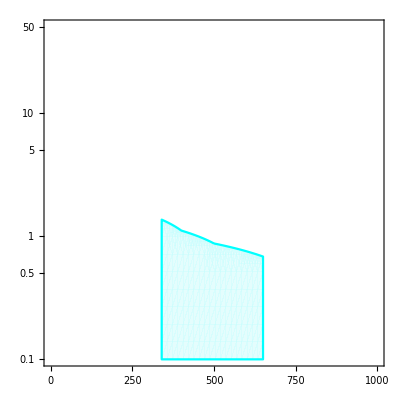

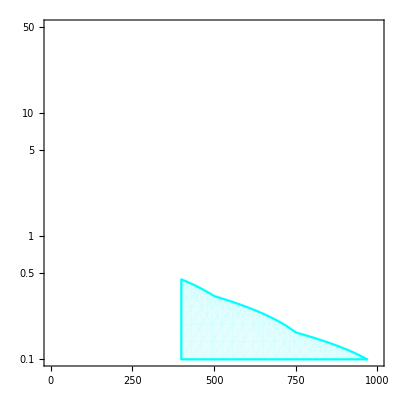

```mathematica
fig4t=RegionPlot[fun4t2[x,y]>12.6,{x,340,650},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
fig4t=RegionPlot[fun4t2[x,y]>ATLAS4t[x],{x,400,1000},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

```mathematica
fig4t=RegionPlot[fun4t2[x,y]>12.6,{x,340,650},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

-Graphics-

InterpolatingFunction::dmval: Input value {1010.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1010.,-0.928974} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1010.,-0.786923} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

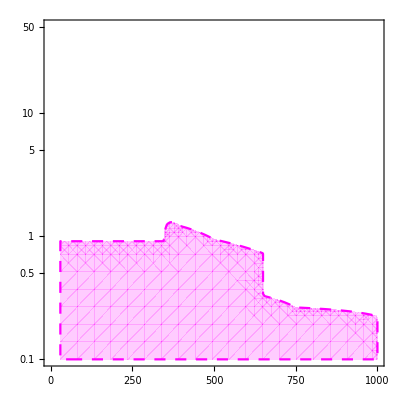

```mathematica
fun4t1[x_,y_]:=Log10[1/1.1]-y;
fun4t[x_,y_]:=If[x<345,fun4t1[x,y],If[x>345&&x<650,fun4t2CMS[x,y],If[x>650,fun4t2ATLAS[x,y],100]]]
fcolA=Directive[Magenta,Opacity[0.2] ];
d=8;
lcolA=Directive[AbsoluteDashing[{d,15-d}],Magenta];
fig4t=RegionPlot[fun4t[x,y]>0,{x,30,1010},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

#### Att

```mathematica
cba=0.1;
sba=√(1-cba cba);
fun4t2[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH]
CMS4t[mH_]:=12.6; 
ATLAS4t[mH_]:=90+(90-25)/600*(mH-400)
fun4t2CMS[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH] funcHtt[mH,tb]-CMS4t[mH];
fun4t2ATLAS[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH]funcHtt[mH,tb]-ATLAS4t[mH];
```

```mathematica
ATLAS4t[1000]
```

155

```mathematica
mH0=400;tb0=Log10[0.3];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
mH0=700;tb0=Log10[0.3];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
mH0=900;tb0=Log10[0.3];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
```

219.43

58.0871

24.5662

```mathematica
mH0=1000;tb0=Log10[0.25];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]+fun4t2[mH0,tb0] funcHtt[mH0,tb0]
```

37.7921

```mathematica
mH0=400;tb0=Log10[0.5];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
mH0=700;tb0=Log10[0.5];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
mH0=1000;tb0=Log10[0.5];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
```

78.9666

20.8873

5.02304

```mathematica
mH0=400;tb0=Log10[1];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
mH0=700;tb0=Log10[1];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
mH0=1000;tb0=Log10[1];
fun4t2[mH0,tb0] funcAtt[mH0,tb0]
```

19.7019

5.19269

1.24086

```mathematica
funcHtt[1000,Log10[1.1]]
```

0.874351

```mathematica
fig4t=RegionPlot[fun4t2[x,y]>12.6,{x,340,650},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
fig4t=RegionPlot[fun4t2[x,y]>ATLAS4t[x],{x,400,1000},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

-Graphics-

-Graphics-

```mathematica
fig4t=RegionPlot[fun4t2[x,y]>12.6,{x,340,650},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

-Graphics-

InterpolatingFunction::dmval: Input value {1010.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

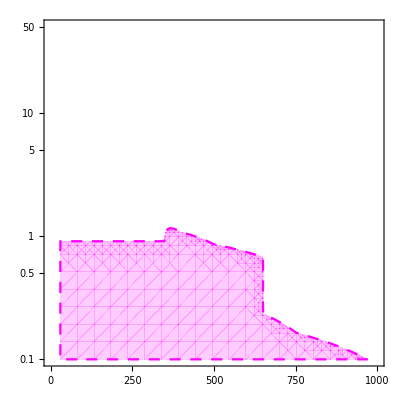

```mathematica
fun4t1[x_,y_]:=Log10[1/1.1]-y;
fun4t[x_,y_]:=If[x<345,fun4t1[x,y],If[x>345&&x<650,fun4t2CMS[x,y],If[x>650,fun4t2ATLAS[x,y],100]]]
fcolA=Directive[Magenta,Opacity[0.2] ];
d=8;
lcolA=Directive[AbsoluteDashing[{d,15-d}],Magenta];
fig4t=RegionPlot[fun4t[x,y]>0,{x,30,1010},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

### Type-I, m_A=m_H, cos(β-α)=0.1,Brhaa

RGBColor[Rational[253, 255], Rational[103, 255], Rational[103, 255]]

RGBColor[Rational[48, 85], Rational[14, 15], Rational[48, 85]]

RGBColor[Rational[9, 17], Rational[206, 255], Rational[50, 51]]

/Users/weisu/Documents/research/project/114a/LHC_HZA/1new_code/My2HDMC0408/data_mh2tb/4top/

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36.0527,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {49.079,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

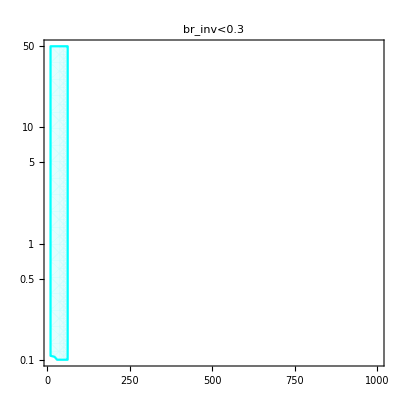

```mathematica
clightred(*fd6767*)=RGBColor[253/255,103/255,103/255]
clightgreen=RGBColor[144/255,238/255,144/255]
clightskyblue=RGBColor[135/255,206/255,250/255]
PathDir=NotebookDirectory[]

(*DEFINE SETUP*)
xmin=10;xmax=1000;ymin=Log10[0.1];ymax=Log10[50];

(*Import Stuff

infile1>>mh>>mH>>mA>>cosba>>tb;5
infile1>>ggA8>>bbA8;2
infile1>>ggA13>>bbA13>>zA13>>wbfA13;4
infile1>>ggH13>>bbH13>>zH13>>wbfH13;4
infile1>>brAtautau>>brAmumu>>brAbb>>brAtt;4
infile1>>brAgg>>brAgaga>>brAzh>>brHtautau;4
infile1>>brHmumu>>brHbb>>brHtt>>brHZZ;4
infile1>>brHWW>>brHhh>>brHgg>>brHgaga;4
infile1>>brhbb>>brHAZ>>brAHZ;3
infile1>>gammatotH>>gammatotA;2
infile1>>ggh13>>bbh13>>WBFh13;3
infile1>>Zh13>>brhaa>>brhHH;3
infile1>>ggA8>>bbA8>>WBFA8>>ZA8;4
infile1>>ggH8>>bbH8>>WBFH8>>ZH8>>gammatoth;5
*)
results=Import["/Users/weisu/Documents/research/project/114a/LHC_HZA/1new_code/My2HDMC0408/data_mh2tb/mh2tb_10.1_noexo.txt","table"];
leng=Length[results];
mH=Table[results[[j,3]],{j,1,leng}];
tb=Table[Log10[results[[j,5]]],{j,1,leng}];
haa=Table[Max[results[[j,41]]+results[[j,42]]],{j,1,leng}];
brHtt=Table[results[[j,26]],{j,1,leng}];

datahaa=Table[{mH[[j]],tb[[j]],haa[[j]]},{j,1,leng} ];


funchaa=Interpolation[datahaa,InterpolationOrder->1];

dataHtt=Table[{mH[[j]],tb[[j]],brHtt[[j]]},{j,1,leng} ];


funcHtt=Interpolation[dataHtt,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[clightcyan,Opacity[0.5] ];lcolA=Cyan;
figbrhaa=RegionPlot[funchaa[x,y]>0.3,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLabel->"br_inv<0.3"]
```

### Type-I, m_A=m_H, cos(β-α)=0.1, ttHtt

```mathematica
ttH[x_]:=If[x≤400,39.48+(19.85-39.48)/100*(x-300),If[x>400 &&x≤500,19.85+(11.62-19.85)/100*(x-400),
If[x>500 &&x≤750,11.62+(3.65-11.62)/250*(x-500),
If[x>750 &&x≤1000,3.65+(1.263-3.65)/250*(x-750),0
]
]
]
];
```

```mathematica
cba=0.1;
sba=√(1-cba cba);
fun4t2[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH]
CMS4t[mH_]:=12.6; 
ATLAS4t[mH_]:=90+(90-25)/600*(mH-400)
fun4t2CMS[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH] funcHtt[mH,tb]-CMS4t[mH];
fun4t2ATLAS[mH_,tb_]:=(cba-sba/10^tb)^2 ttH[mH]funcHtt[mH,tb]-ATLAS4t[mH];
```

```mathematica
funcHtt[1000,Log10[1.1]]
```

0.61359

```mathematica
fig4t=RegionPlot[fun4t2[x,y]>12.6,{x,340,650},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
fig4t=RegionPlot[fun4t2[x,y]>ATLAS4t[x],{x,400,1000},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

-Graphics-

-Graphics-

```mathematica
fig4t=RegionPlot[fun4t2[x,y]>12.6,{x,340,650},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

-Graphics-

InterpolatingFunction::dmval: Input value {1010.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

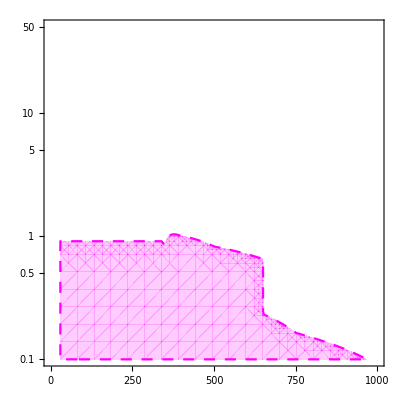

```mathematica
fun4t1[x_,y_]:=Log10[1/1.1]-y;
fun4t[x_,y_]:=If[x<345,fun4t1[x,y],If[x>345&&x<650,fun4t2CMS[x,y],If[x>650,fun4t2ATLAS[x,y],100]]]
fcolA=Directive[Magenta,Opacity[0.2] ];
d=8;
lcolA=Directive[AbsoluteDashing[{d,15-d}],Magenta];
fig4t=RegionPlot[fun4t[x,y]>0,{x,30,1010},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

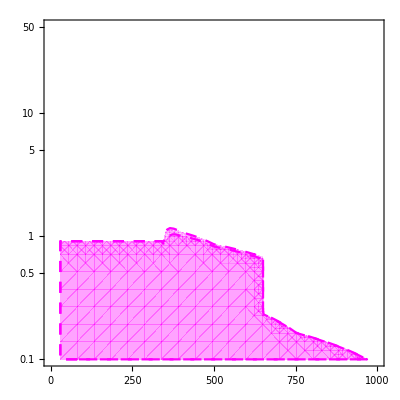

```mathematica
Show[-Graphics-,-Graphics-]
```